## Analytic continuation of β_34

β_34 is unambiguously defined for negative s_34. We would like to analytically continue it to positive s_34. 

One possible definition is

β_34= -1/2Log[(1-v)/(1+v)]

where

v = Sqrt[1-(4 m_t^2)/s_34^2]

Introducing s= s_34/(2 m_t^2), the argument of the Log reads

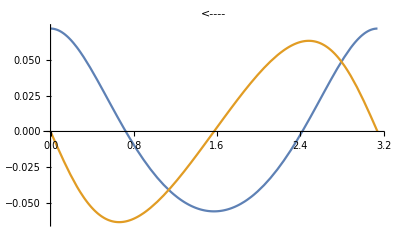

```mathematica
arg[phi_]:=(1-Sqrt[1-1/s^2])/(1+Sqrt[1-1/s^2])/.s-> 2 Exp[I phi]
Plot[{Re[arg[phi]],Im[arg[phi]]},{phi,Pi,0},PlotLabel->"<----"]
```

As we see, it is continuous as we go from negative to positive s, which means that, while doing the analytic continuation, we do not cross any cut, which in, in other words means that we stay in the same Riemann surface.

Let us now look how β_34itself changes as we go from s < 0 to s > 0:

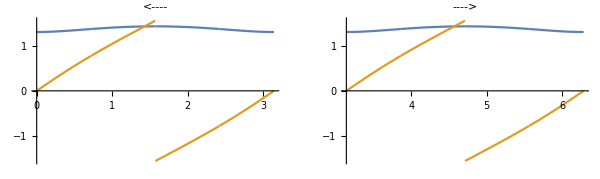

```mathematica
beta34ver1[phi_]:=-1/2 Log[arg[phi]]
p1=Plot[{Re[beta34ver1[phi]],Im[beta34ver1[phi]]},{phi,Pi,0},PlotLabel->"<----"];
p2=Plot[{Re[beta34ver1[phi]],Im[beta34ver1[phi]]},{phi,Pi,2Pi},PlotLabel->"---->"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

As we see, this time, the imaginary part has a discontinuity along ϕ=π/2, 3π/4. This means that, while making a turn, we enter another Riemann surface and our result acquires -π i, if we cross the cut in the upper half-plane or +π i, if we cross if we go from below real axis.

Let’s look at the same function β_34 but expresses through β = Sqrt[1-(4 m_t^2)/(s_34+2 m_t^2)] = Sqrt[(s-1)/(s+1)]

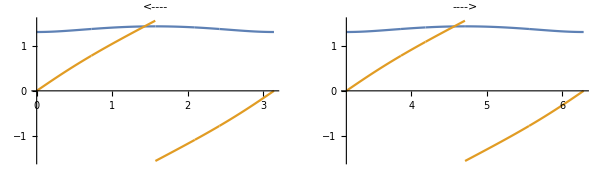

```mathematica
beta34ver2[phi_]:=-1/2 Log[(beta^2-2beta+1)/(1+beta)^2]/.beta-> Sqrt[(s-1)/(s+1)]/.s-> 2 Exp[I phi]
p1=Plot[{Re[beta34ver2[phi]],Im[beta34ver2[phi]]},{phi,Pi,0},PlotLabel->"<----"];
p2=Plot[{Re[beta34ver2[phi]],Im[beta34ver2[phi]]},{phi,Pi,2Pi},PlotLabel->"---->"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

As shown in the above plots, we arrive at exactly the same conclusion: going above brings -π i, going below brings +π i.

Finally, there is an alternative form

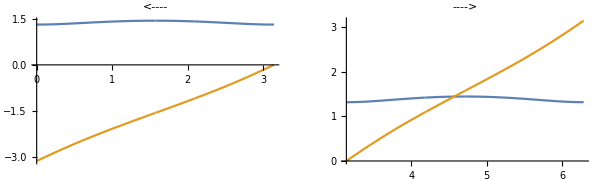

```mathematica
beta34ver3[phi_]:=-Log[(-1+beta)/(1+beta)]/.beta-> Sqrt[(s-1)/(s+1)]/.s-> 2 Exp[I phi]
p1=Plot[{Re[beta34ver3[phi]],Im[beta34ver3[phi]]},{phi,Pi,0},PlotLabel->"<----"];
p2=Plot[{Re[beta34ver3[phi]],Im[beta34ver3[phi]]},{phi,Pi,2Pi},PlotLabel->"---->"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

The beta34 function can be also determined directly from the definition. We can choose the argument like below and than continue in the lower half plane (because with this choice of argument we effectively have -i ep prescription) from phi = 0 to phi = -pi:

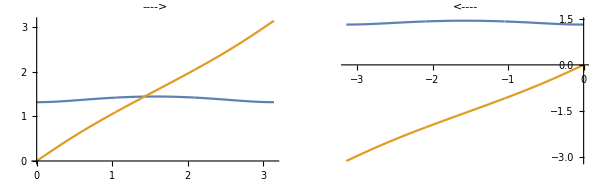

```mathematica
f[phi_]:=ArcCosh[2Exp[I phi]]
p1=Plot[{Re[f[phi]],Im[f[phi]]},{phi,0,Pi},PlotLabel->"---->"];
p2=Plot[{Re[f[phi]],Im[f[phi]]},{phi,0,-Pi},PlotLabel->"<----"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

or choose the argument like that and then continue in the upper half-plane from phi = pi to 0:

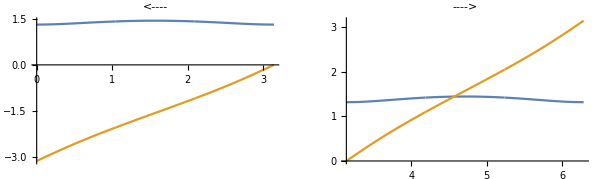

```mathematica
f[phi_]:=ArcCosh[-2Exp[I phi]]
p1=Plot[{Re[f[phi]],Im[f[phi]]},{phi,Pi,0},PlotLabel->"<----"];
p2=Plot[{Re[f[phi]],Im[f[phi]]},{phi,Pi,2Pi},PlotLabel->"---->"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

The arcosh function in 3D plots:

```mathematica
Plot3D[Im[ArcCosh[-(x+ I y)]],{x,-4,4},{y,-4,4},AxesLabel->{"x","y"}]
```

-Graphics3D-

```mathematica
Plot3D[Re[ArcCosh[-(x+ I y)]],{x,-4,4},{y,-4,4},AxesLabel->{"x","y"}]
```

-Graphics3D-

## Coth, Log and PolyLog

Here we want to check if the function that appear in velocity-dependent AD are continuous while performing the rotation from negative to positive s.

Let’s notice that arguments of Li2, Li3 and Log  ∈ [0,1] in the space-like region:

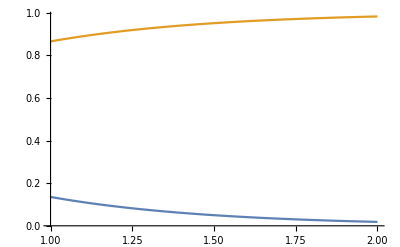

```mathematica
Plot[{Exp[-2beta34],1-Exp[-2beta34]},{beta34,1,2},PlotRange->All]
```

Hence, these functions do not need any continuation and we can directly obtain

```mathematica
Coth[beta34]/.beta34-> 1/2 Log[((1+beta)/(1-beta))^2]//FullSimplify
```

(1+beta^2)/(2 beta)

```mathematica
Log[1-Exp[-2beta34]]/.beta34-> 1/2 Log[((1+beta)/(1-beta))^2]//Simplify
```

Log[(4 beta)/(1+beta)^2]

```mathematica
PolyLog[2,Exp[-2beta34]]/.beta34-> 1/2 Log[((1+beta)/(1-beta))^2]//Simplify
```

PolyLog[2,(-1+beta)^2/(1+beta)^2]

Indeed our functions do not develop discontinuity as we go to time-like case:

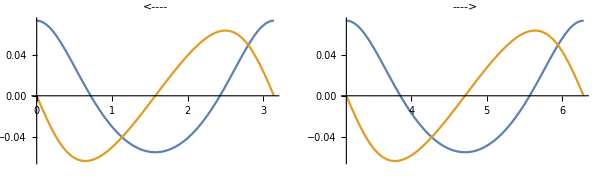

```mathematica
Li2[phi_]:=PolyLog[2,Exp[-2beta34ver1[phi]]]
p1=Plot[{Re[Li2[phi]],Im[Li2[phi]]},{phi,Pi,0},PlotLabel->"<----"];
p2=Plot[{Re[Li2[phi]],Im[Li2[phi]]},{phi,Pi,2Pi},PlotLabel->"---->"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

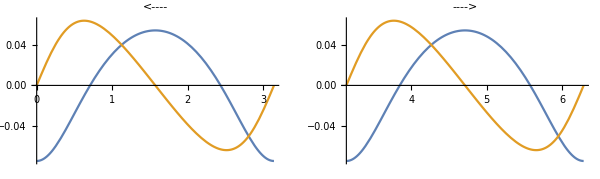

```mathematica
f[phi_]:=Log[1-Exp[-2beta34ver1[phi]]]
(*f[phi_]=Log[(4 beta)/(1+beta)^2]/.beta-> Sqrt[(s-1)/(s+1)](*/.s-> 2 Exp[I phi]*)*)
p1=Plot[{Re[f[phi]],Im[f[phi]]},{phi,Pi,0},PlotLabel->"<----"];
p2=Plot[{Re[f[phi]],Im[f[phi]]},{phi,Pi,2Pi},PlotLabel->"---->"];
GraphicsGrid[{{p1,p2}},ImageSize->600]
```

This is because changing sign of s corresponds to rotation around 0 whereas the functions given above have branch point at 1.

## Transformation β_34 → -β_34 in velocity-dependent AD

```mathematica
Get["QCDFunctions`"]
```

```mathematica
ReplContinuationPolyLog = {PolyLog[2,z_]-> -PolyLog[2,1/z]-1/2 Log[-z]^2-π^2/6,PolyLog[3,z_]-> PolyLog[3,1/z]-1/6 Log[-z]^3-π^2/6 Log[-z]};
ReplContinuationLog = {Log[z_]-> Log[-z] +π I};
(*ReplContinuationLog = {Log[z_]-> Log[-z] - π I};*)
```

```mathematica
Collect[gammacuspvel1[beta34],Coth[beta34]]
```

8 beta34^2 CA+(4 CA π^2)/3+Coth[beta34] (beta34 (4 CA (67/9-π^2/3)-(80 nf TF)/9)+8 CA (-beta34^2-beta34^3/3-1/6 (1+beta34) π^2-2 beta34 Log[1-ⅇ^(-2 beta34)]+PolyLog[2,ⅇ^(-2 beta34)]))+8 CA Coth[beta34]^2 (beta34^3/3+(beta34 π^2)/6+beta34 PolyLog[2,ⅇ^(-2 beta34)]+PolyLog[3,ⅇ^(-2 beta34)]-Zeta[3])+8 CA Zeta[3]

```mathematica
gammanegative = gammacuspvel1[beta34]/.beta34-> -beta34/.ReplContinuationPolyLog/.ReplContinuationLog/.{Log[-1+ⅇ^(2 beta34)]-> LOG[1-ⅇ^(-2 beta34)]+ Log[ⅇ^(2 beta34)]}/.LOG-> Log;
gammanegative=Collect[Simplify[gammanegative, Assumptions->{beta34>0}],Coth[beta34]]
```

8 beta34^2 CA+(4 CA π^2)/3+Coth[beta34] (-8 beta34^2 CA-(8 beta34^3 CA)/3-(4 CA π^2)/3-4/3 beta34 CA π^2-4/9 beta34 (CA (-67+3 π^2)+20 nf TF)-16 beta34 CA Log[1-ⅇ^(-2 beta34)]+8 CA PolyLog[2,ⅇ^(-2 beta34)])+8 CA Zeta[3]+Coth[beta34]^2 ((8 beta34^3 CA)/3+4/3 beta34 CA π^2+8 beta34 CA PolyLog[2,ⅇ^(-2 beta34)]+8 CA PolyLog[3,ⅇ^(-2 beta34)]-8 CA Zeta[3])

```mathematica
gammacuspvel1[beta34]-gammanegative//Expand
```

0